## Import dati

```mathematica
Clear[a,b,c];
a=Import[NotebookDirectory[]<>"meas_noPerm_chi16.dat"];
d=Import[NotebookDirectory[]<>"meas_noPerm_chi8_add.dat"];
b=Import[NotebookDirectory[]<>"meas_noMC_chi20_N250.dat"];
c=Import[NotebookDirectory[]<>"meas_vecRho_qtech.dat"];
e=Import[NotebookDirectory[]<>"meas_noPerm_chi8_norm.dat"];
```

```mathematica
a[[1]]
```

{#,time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

```mathematica
d[[1]]
```

{#,time,N_11,N_2,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

```mathematica
b[[1]]
```

{#,time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,Sx_1,Sz_1,re_over,im_over}

```mathematica
c[[1]]
```

{#,time,Norm_1,vecN_11,vecN_21,vecN_31,vecN_41,vecN_51,vecN_61,vecN_71,vecN_81,vecN_82,vecN_83,vecN_84,vecN_85,vecN_86,vecN_87,vecÏ.83x_1,vecÏ.83z_1,re_over,im_over,Norm}

```mathematica
e[[1]]
```

{#,time,N_11,N_2,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

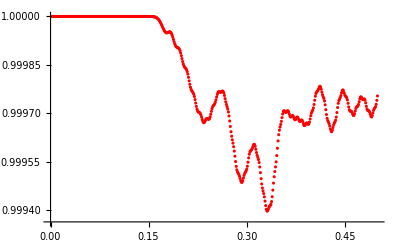

```mathematica
ListPlot[Transpose[{Drop[e[[All,1]],1],Drop[e[[All,-1]],1]}] ,PlotStyle->Red]
```

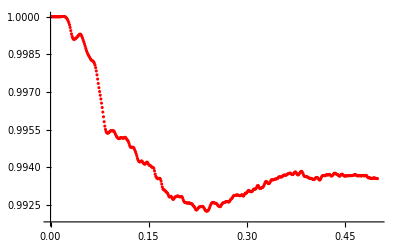

```mathematica
Clear[normMCFullLind];
normMCFullLind = ListPlot[Transpose[{Drop[c[[All,1]],1],Drop[c[[All,2]],1]}] ,PlotStyle->Red]
```

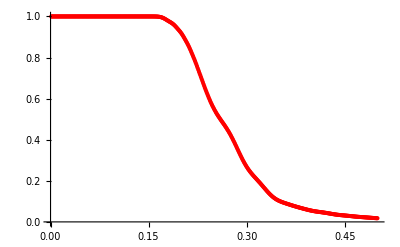

```mathematica
Clear[normMCEff];
normMCEff = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,-1]],1]^2}] ,PlotStyle->Red]
```

## ⟨σz⟩

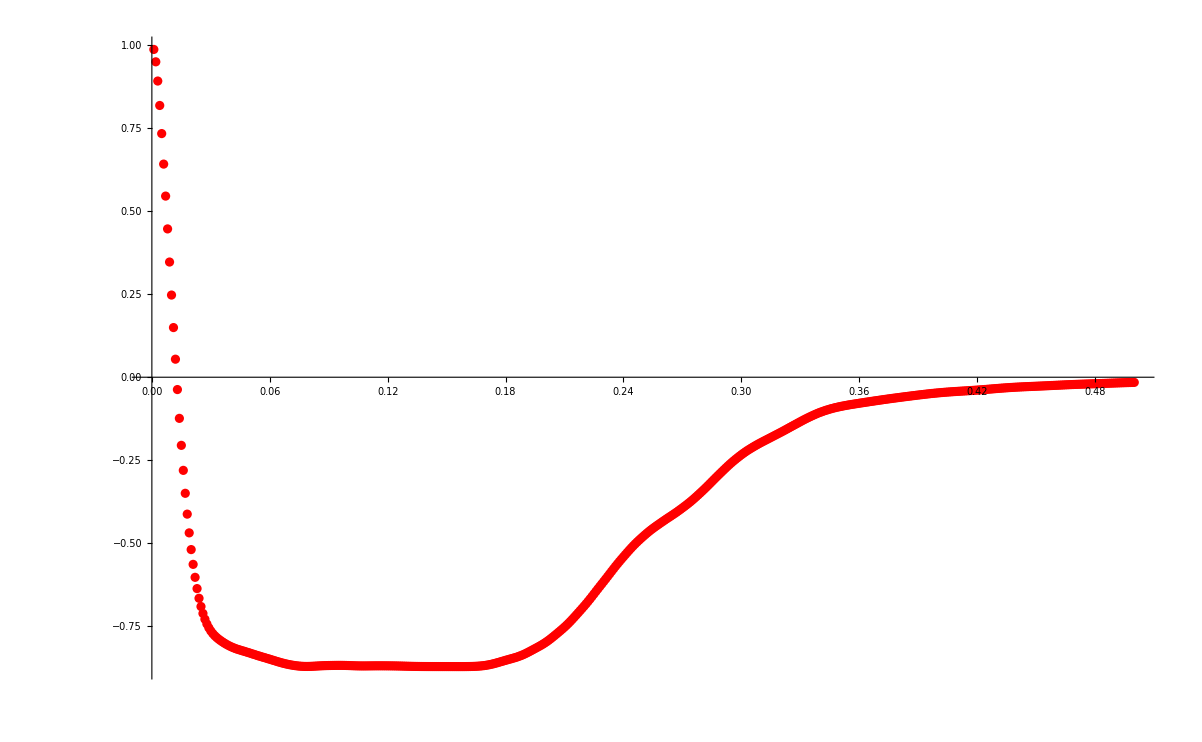

```mathematica
sz = ListPlot[Transpose[{Drop[a[[All, 1]], 1],2(Drop[a[[All, -4]], 1])(*/Drop[a[[All, -1]], 1]^2*)}], PlotStyle -> Red, PlotRange -> All]
```

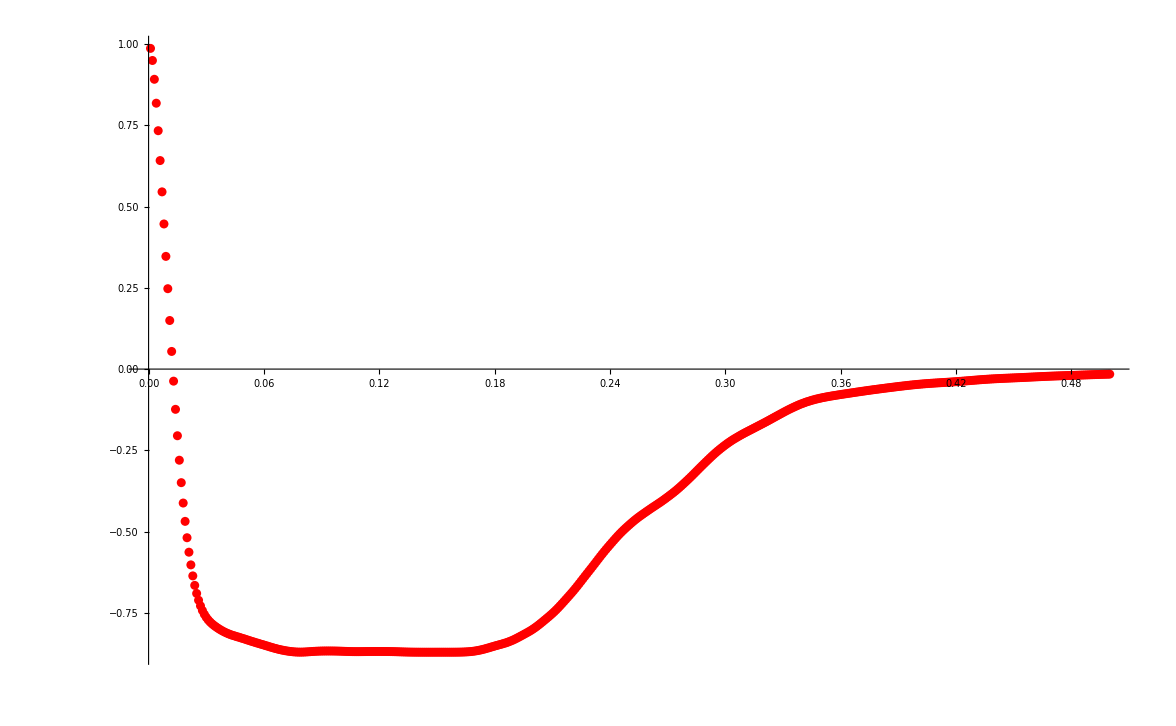

```mathematica
szAdd = ListPlot[Transpose[{Drop[d[[All, 1]], 1],2(Drop[d[[All, -4]], 1])(*/Drop[a[[All, -1]], 1]^2*)}], PlotStyle -> Red, PlotRange -> All]
```

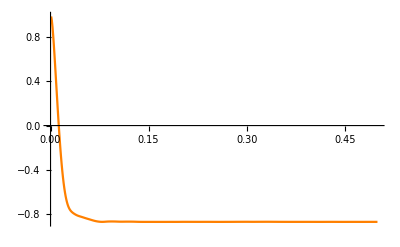

```mathematica
szNorm = ListPlot[Transpose[{Drop[e[[All, 1]], 1],2(Drop[e[[All, -4]], 1])(*/Drop[d[[All, -1]], 1]^2*)}], PlotStyle -> Orange, PlotRange -> All,Joined->True]
```

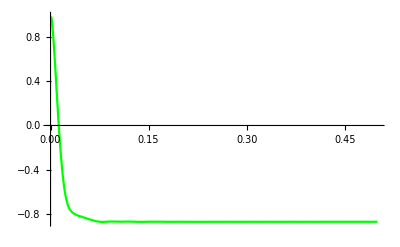

```mathematica
szVec = ListPlot[Transpose[{Drop[c[[All,1]],1],Drop[c[[All,-4]],1]/Drop[c[[All,2]],1]}],PlotStyle->Green,PlotRange->All,Joined->True]
```

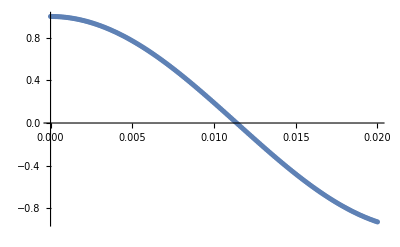

```mathematica
szFree=ListPlot[Table[{t,
state = MatrixExp[-ⅈ t 69*PauliMatrix[1]].{1,0};
Conjugate[state].PauliMatrix[3].state},{t,0,0.02,0.0001}]
]
```

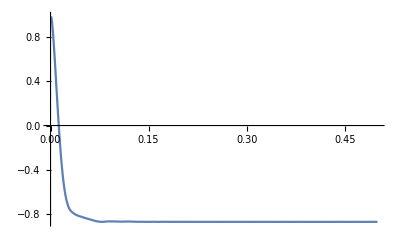

```mathematica
szRef = ListPlot[Transpose[{b[[All,1]],2 b[[All,-3]]}],PlotRange->All,Joined->True]
```

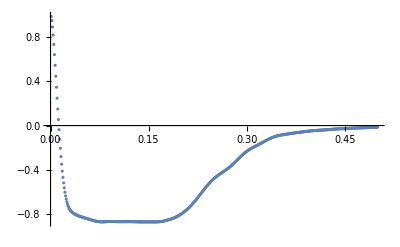

```mathematica
szRefAdd = ListPlot[Transpose[{d[[All,1]],2 d[[All,-4]]}],PlotRange->All]
```

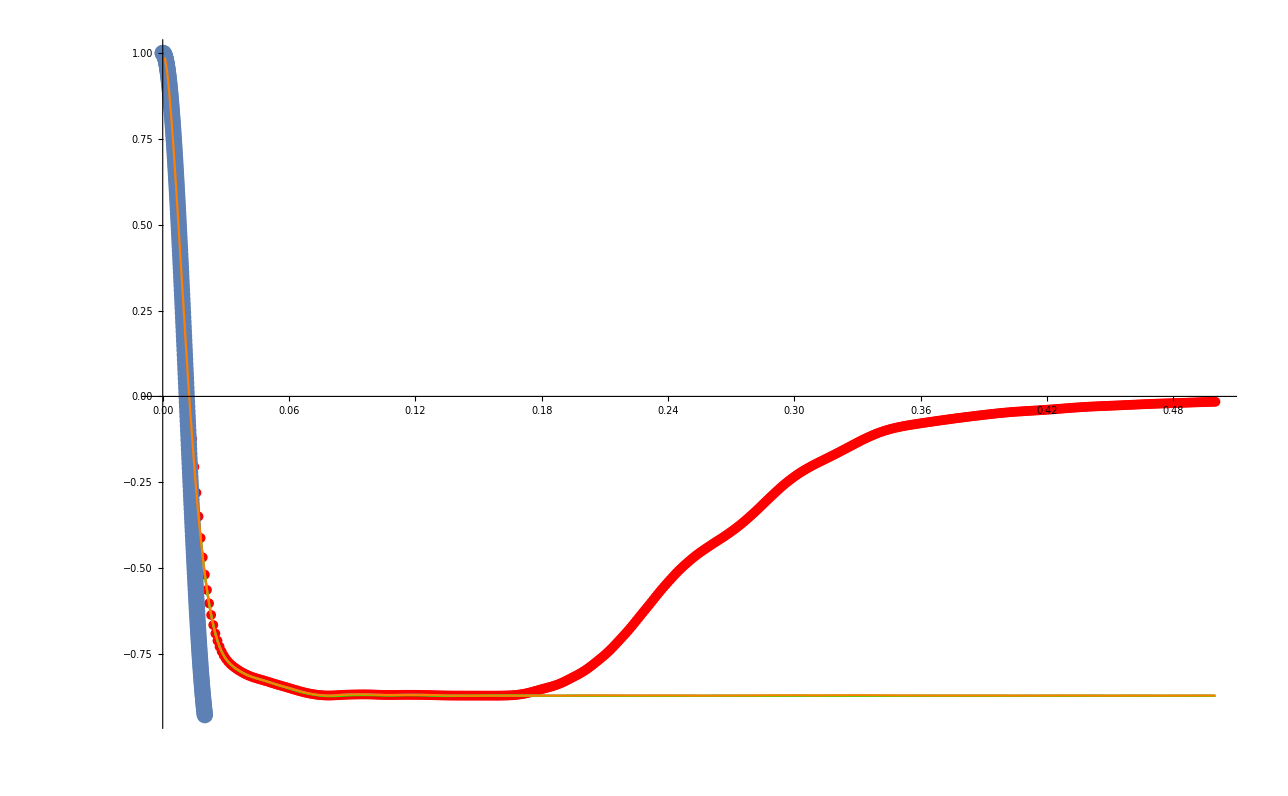

```mathematica
Show[sz,szRef,szVec,szFree,szNorm, PlotRange->All]
```

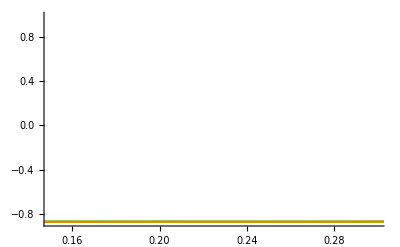

```mathematica
Show[szRef,szVec,szNorm, PlotRange->{{0.15,0.3},All}]
```

## ⟨N_1⟩

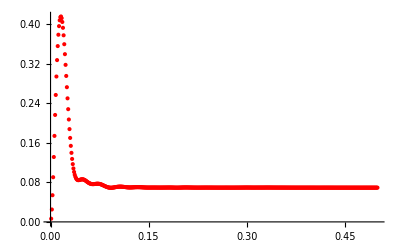

```mathematica
Clear[n1];
n1 = ListPlot[Transpose[{Drop[d[[All,1]],1],Drop[d[[All,3]],1]/Drop[d[[All,-1]],1]^2}],PlotStyle->Red,PlotRange->All]
```

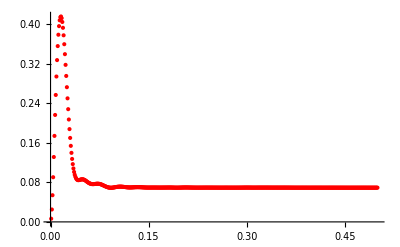

```mathematica
Clear[n1Norm];
n1Norm = ListPlot[Transpose[{Drop[e[[All,1]],1],Drop[e[[All,3]],1]}],PlotStyle->Red,PlotRange->All]
```

```mathematica
(*Clear[n1Ref];
n1Ref = ListPlot[Transpose[{b[[All,1]], b[[All,2]]}],PlotRange->All]*)
```

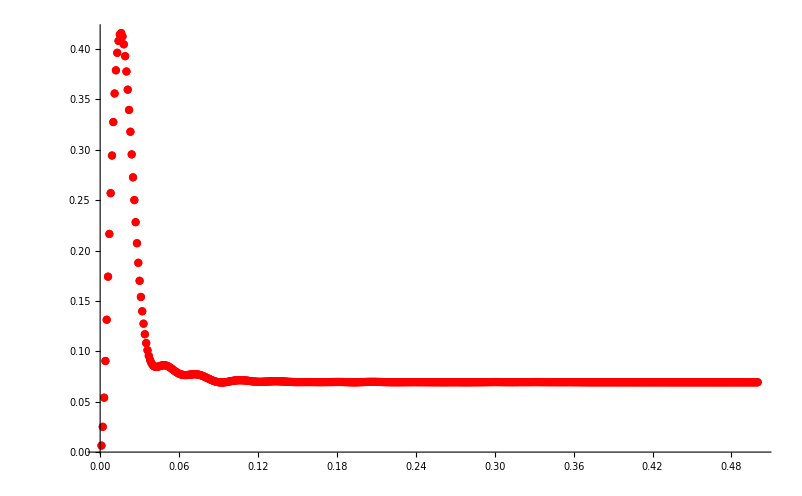

```mathematica
Show[n1,n1Norm,PlotRange->All]
```

## ⟨N_11⟩

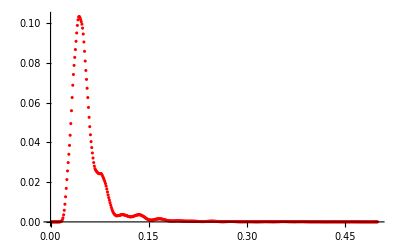

```mathematica
Clear[n11];
n11 = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,2]],1]/Drop[a[[All,-1]],1]^2}],PlotStyle->Red,PlotRange->All]
```

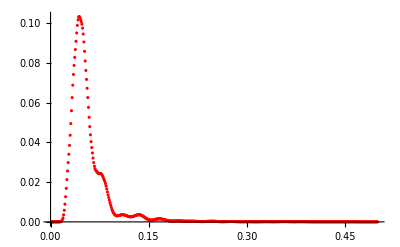

```mathematica
Clear[n11Norm];
n11Norm = ListPlot[Transpose[{Drop[e[[All,1]],1],Drop[e[[All,2]],1](*/Drop[a[[All,-1]],1]^2*)}],PlotStyle->Red,PlotRange->All]
```

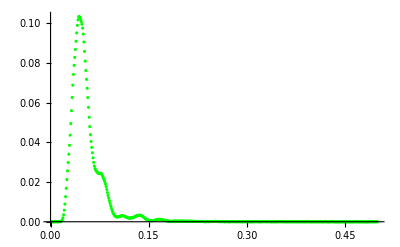

```mathematica
Clear[n11Vec];
n11Vec = ListPlot[Transpose[{Drop[c[[All,1]],1],Drop[c[[All,3]],1]/Drop[c[[All,2]],1]^2}],PlotStyle->Green,PlotRange->All]
```

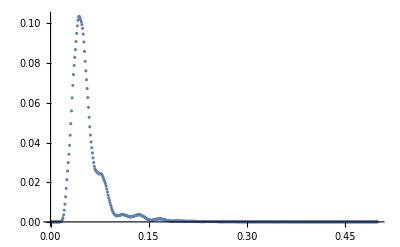

```mathematica
Clear[n11Ref];
n11Ref = ListPlot[Transpose[{b[[All,1]], b[[All,2]]}],PlotRange->All]
```

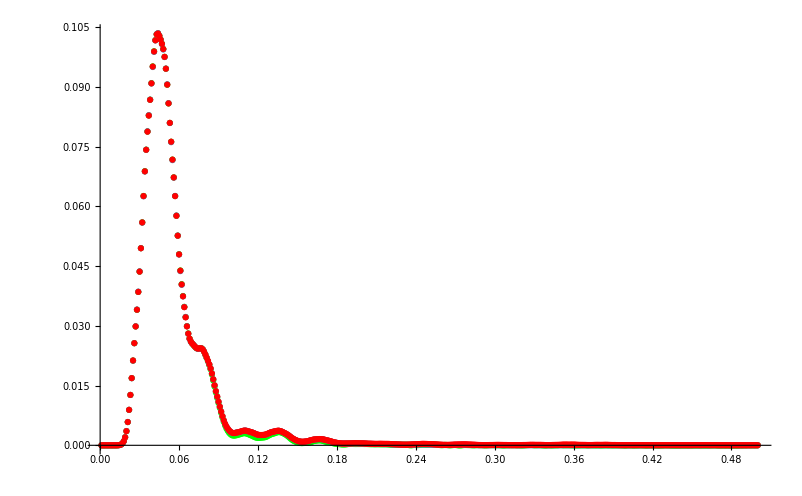

```mathematica
Show[n11,n11Vec,n11Ref,n11Norm, PlotRange->All]
```

## ⟨N_41⟩

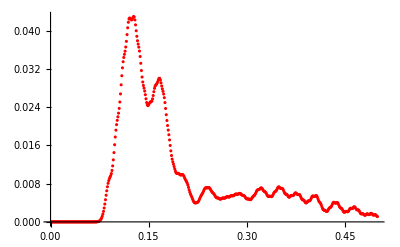

```mathematica
Clear[n41];
n41 = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,5]],1]/Drop[a[[All,-1]],1]^2}],PlotStyle->Red,PlotRange->All]
```

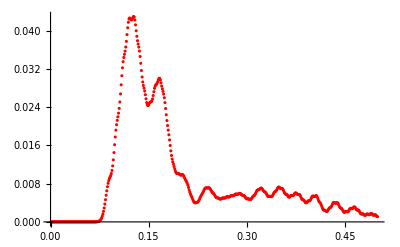

```mathematica
Clear[n41Norm];
n41Norm = ListPlot[Transpose[{Drop[e[[All,1]],1],Drop[e[[All,6]],1]}],PlotStyle->Red,PlotRange->All]
```

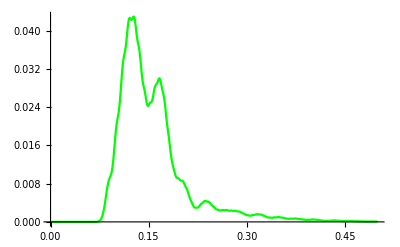

```mathematica
Clear[n41Vec];
n41Vec = ListPlot[Transpose[{Drop[c[[All,1]],1],Drop[c[[All,6]],1]/Drop[c[[All,2]],1]}],PlotStyle->Green,PlotRange->All,Joined->True]
```

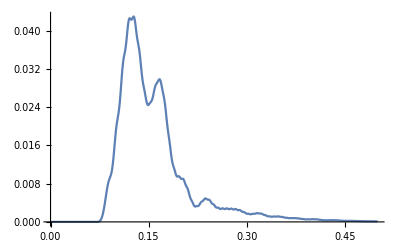

```mathematica
Clear[n41Ref];
n41Ref = ListPlot[Transpose[{b[[All,1]], b[[All,5]]}],PlotRange->All,Joined->True]
```

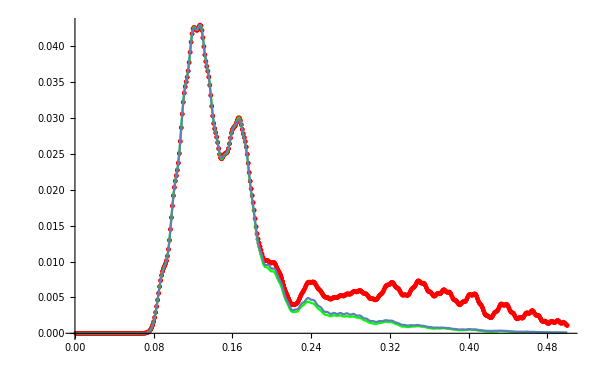

```mathematica
Show[n41,n41Norm,n41Vec,n41Ref,PlotRange->All]
```

## ⟨N_81⟩

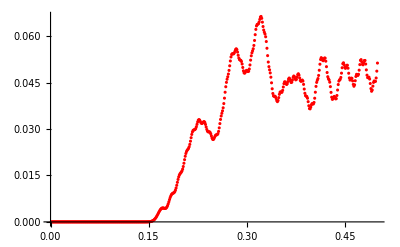

```mathematica
Clear[n81];
n81 = ListPlot[Transpose[{Drop[a[[All,1]],1],Drop[a[[All,9]],1]/Drop[a[[All,-1]],1]^2}],PlotStyle->Red,PlotRange->All]
```

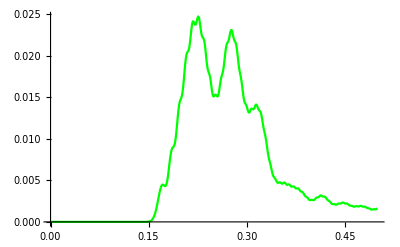

```mathematica
Clear[n81Vec];
n81Vec = ListPlot[Transpose[{Drop[c[[All,1]],1],Drop[c[[All,-12]],1]/Drop[c[[All,2]],1]^2}],PlotStyle->Green,PlotRange->All,Joined->True]
```

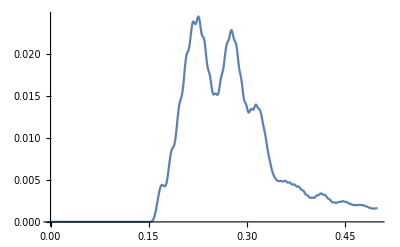

```mathematica
Clear[n81Ref];
n81Ref = ListPlot[Transpose[{b[[All,1]], b[[All,-5]]}],PlotRange->All,Joined->True]
```

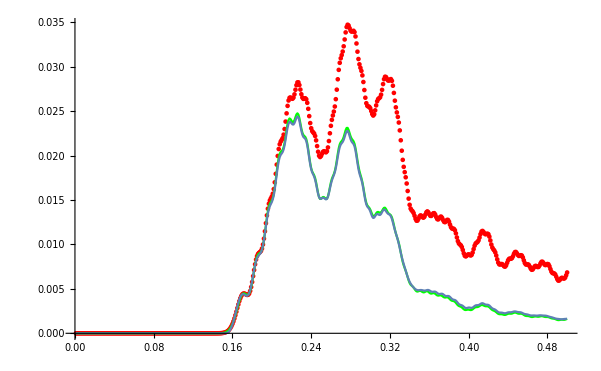

```mathematica
Show[n81,n81Vec,n81Ref,PlotRange->All]
```